```mathematica
h[x_]:=Piecewise[{{1+Subscript[c, 0,1] x+Subscript[c, 0,2] x^2+Subscript[c, 0,3] x^3+Subscript[c, 0,4] x^4, 0≤x≤1/2}, {Subscript[c, 1,1](x-1)+Subscript[c, 1,2](x-1)^2+Subscript[c, 1,3](x-1)^3+Subscript[c, 1,4](x-1)^4, 1/2<x≤3/2}, {Subscript[c, 2,1](x-2)+Subscript[c, 2,2](x-2)^2+Subscript[c, 2,3](x-2)^3+Subscript[c, 2,4](x-2)^4, 3/2<x≤5/2}, {0, True}}];
f[x_]:=h[Abs[x]];
AllVars={Subscript[c, 0,1],Subscript[c, 0,2],Subscript[c, 0,3],Subscript[c, 0,4],Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3],Subscript[c, 1,4],Subscript[c, 2,1],Subscript[c, 2,2],Subscript[c, 2,3],Subscript[c, 2,4]};
```

```mathematica
(*Continuity*)
C1=Limit[h[x],x->1/2,Direction->1]==Limit[h[x],x->1/2,Direction->-1]
C2=Limit[h[x],x->3/2,Direction->1]==Limit[h[x],x->3/2,Direction->-1]
C3=Limit[h[x],x->5/2,Direction->1]==Limit[h[x],x->5/2,Direction->-1]
```

1/16 (16+8 c_(0,1)+4 c_(0,2)+2 c_(0,3)+c_(0,4))==1/16 (-8 c_(1,1)+4 c_(1,2)-2 c_(1,3)+c_(1,4))

1/16 (8 c_(1,1)+4 c_(1,2)+2 c_(1,3)+c_(1,4))==1/16 (-8 c_(2,1)+4 c_(2,2)-2 c_(2,3)+c_(2,4))

1/16 (8 c_(2,1)+4 c_(2,2)+2 c_(2,3)+c_(2,4))==0

```mathematica
(*Partition of unity and linear term*)
T0=CoefficientList[FullSimplify[∑_(i=-6)^6 f[x-i],x>0&&x<1/2],x]
T1=CoefficientList[FullSimplify[∑_(i=-6)^6 i f[x-i],x>0&&x<1/2],x]
```

{1,c_(0,1),c_(0,2)+2 (c_(1,2)+c_(2,2)),c_(0,3),c_(0,4)+2 (c_(1,4)+c_(2,4))}

{0,-2 c_(1,1)-4 c_(2,1),0,-2 (c_(1,3)+2 c_(2,3))}

```mathematica
(*Smoothness*)
Dh=Simplify[D[h[x],x],x>0];
S0=(Dh/.x->0)==0
S1=Limit[Dh,x->1/2,Direction->1]==Limit[Dh,x->1/2,Direction->-1]
S2=Limit[Dh,x->3/2,Direction->1]==Limit[Dh,x->3/2,Direction->-1]
S3=Limit[Dh,x->5/2,Direction->1]==Limit[Dh,x->5/2,Direction->-1]
```

c_(0,1)==0

c_(0,1)+c_(0,2)+(3 c_(0,3))/4+(c_(0,4))/2==c_(1,1)-c_(1,2)+(3 c_(1,3))/4-(c_(1,4))/2

c_(1,1)+c_(1,2)+(3 c_(1,3))/4+(c_(1,4))/2==c_(2,1)-c_(2,2)+(3 c_(2,3))/4-(c_(2,4))/2

c_(2,1)+c_(2,2)+(3 c_(2,3))/4+(c_(2,4))/2==0

```mathematica
GenSols=Solve[{
	C1,C2,C3,
	T0[[2]]==0,
	T0[[3]]==0,
	T0[[4]]==0,
	T0[[5]]==0,
	T1[[2]]==1,
	T1[[4]]==0,
	S0,S1,S2,S3
	},
	AllVars
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_(0,1)→0,c_(0,3)→0,c_(1,1)→-13/6-(11 c_(0,2))/12-(13 c_(0,4))/48,c_(1,2)→13/6+(2 c_(0,2))/3+(c_(0,4))/3,c_(1,3)→8/3+(5 c_(0,2))/3+(7 c_(0,4))/12,c_(1,4)→-14/3-(8 c_(0,2))/3-(4 c_(0,4))/3,c_(2,1)→5/6+(11 c_(0,2))/24+(13 c_(0,4))/96,c_(2,2)→-13/6-(7 c_(0,2))/6-(c_(0,4))/3,c_(2,3)→-4/3-(5 c_(0,2))/6-(7 c_(0,4))/24,c_(2,4)→14/3+(8 c_(0,2))/3+(5 c_(0,4))/6}}

```mathematica
RegionXY[k_]:={Quotient[k,2],1+Quotient[-k,2]};
Regions=Table[RegionXY[k],{k,-4,7}]-1/2
```

{{-5/2,5/2},{-5/2,3/2},{-3/2,3/2},{-3/2,1/2},{-1/2,1/2},{-1/2,-1/2},{1/2,-1/2},{1/2,-3/2},{3/2,-3/2},{3/2,-5/2},{5/2,-5/2},{5/2,-7/2}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
φ=1/2;
W[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF=∑_(i=-5)^6 ∑_(j=-5)^6 W[i-j]f[x-i,y-j]/.GenSol;
SimplifySquare[f_,x0_,y0_]:=Simplify[f,x>x0&&x<x0+1&&y>y0&&y<y0+1];
DSimplifySquare[f_,{x0_,y0_}]:=Simplify[D[SimplifySquare[f,x0,y0],{{x,y}}]];
DSumF=ParallelMap[DSimplifySquare[SumF,#]&,Regions];
```

```mathematica
AnisoInt[df_,{x0_,y0_}]:=Simplify[Integrate[Expand[(df.{1,1})^2],{x,x0,x0+1},{y,y0,y0+1}]];
AnisoInts=Parallelize[MapThread[AnisoInt,{DSumF,Regions}]];
Err=Simplify[Total[AnisoInts]]
```

1/5618427494400(30138878443520+589736057600 c_(0,2)^4+13767277232128 c_(0,4)+2205392332800 c_(0,4)^2+136508262112 c_(0,4)^3+3241946411 c_(0,4)^4+256 c_(0,2)^3 (27664541552+2442488383 c_(0,4))+96 c_(0,2)^2 (315593557760+58816453520 c_(0,4)+2632493507 c_(0,4)^2)+16 c_(0,2) (3203480279552+1015838792832 c_(0,4)+94651470240 c_(0,4)^2+2890448743 c_(0,4)^3))

```mathematica
FreeVars=Variables[Err];
DErr=Simplify[D[Err,{FreeVars}]];
H=D[DErr,{FreeVars}];
Sols=Solve[DErr==0,FreeVars,Reals];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1 | 0.0690686 | True

```mathematica
RootReduce[Sols[[1]]]
```

{c_(0,2)→Root[1689662005856337976240041904499715134372237013891+1913730991673238426329051917073993219776357823234 #1+875576459165396432047441848633307153441108337957 #1^2+220353172042287473274228459981792313551037813848 #1^3+34801416482455760933198507141290225454678189258 #1^4+3691137740398847524505779769450660705708056556 #1^5+269781047608097129415603204681660622987864608 #1^6+13495678805173790703538473545709318352456896 #1^7+431424428610766564410277417438563815617152 #1^8+7052647884593722360448514392761188016896 #1^9&,1],c_(0,4)→Root[-12052730059666565027942383263597277906151992998912+8724149967135470183666169667339895553162816345600 #1-2307186105966193393075892682083728786314507275328 #1^2+291580584404141632572557804308371318670966217856 #1^3-19458521328012163527706445700672395426531724968 #1^4+806520397583283384374587130856734796383219852 #1^5-21683052237286257632433005453889060211834536 #1^6+387555349882436704314878114069617899997788 #1^7-4358609338880559588643958975730339962778 #1^8+27549405799194227970502009346723390691 #1^9&,1]}

{c_(0,1)→0,c_(0,3)→0,c_(1,1)→-0.828758,c_(1,2)→1.62969,c_(1,3)→0.524805,c_(1,4)→-2.51876,c_(2,1)→0.164379,c_(2,2)→-0.427537,c_(2,3)→-0.262402,c_(2,4)→0.919919,c_(0,2)→-2.40431,c_(0,4)→3.19769}

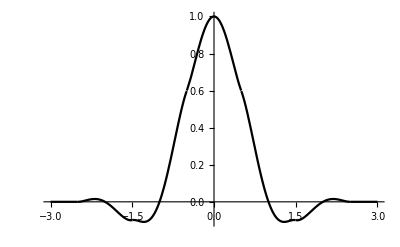

```mathematica
NSol=N[Sols[[1]]];
FullSol=Join[GenSol/.NSol,NSol]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```